```mathematica
refVol=Abs[Partition[BinaryReadList[NotebookDirectory[]<>"../test_data/8mm_iso_x_rot_0_5_to_2_5_deg_z_trans_rep_0_slice_"<>ToString[#]<>".dat","Complex64"],32]&/@Range[0,31,1]];
```

```mathematica
scale=1/Max[refVol]
```

15.3553

```mathematica
refVolScaled=scale * refVol;
```

```mathematica
BinaryWrite[NotebookDirectory[]<>"refVolInput.dat",refVolScaled,"Real64"];
```

```mathematica
newVolScaled=scale * Abs[Partition[BinaryReadList[NotebookDirectory[]<>"../test_data/8mm_iso_x_rot_0_5_to_2_5_deg_z_trans_rep_5_slice_"<>ToString[#]<>".dat","Complex64"],32]&/@Range[0,31,1]];
```

```mathematica
BinaryWrite[NotebookDirectory[]<>"newVolInput.dat",newVolScaled,"Real64"];
```

Compute the cooridinates of each point in the Fourier domain; note that Fourier coordinates are funny in that the origin is centered in the first voxel

```mathematica
fourierPoints=Function[{zDim,yDim,xDim},RotateLeft[Table[{i,j,k},{i,-zDim,zDim-1},{j,-yDim,yDim-1},{k,-xDim,xDim-1}],{zDim,yDim,xDim}]]@@(Dimensions[refVolScaled]/2);
```

```mathematica
Dimensions[fourierPoints]
```

{32,32,32,3}

Define the radial window function that will be applied in the Fourier domain

```mathematica
windowFunction[x_]:=If[x/16<0.75,1,CosineWindow[(x/16-0.75)/0.375]]
```

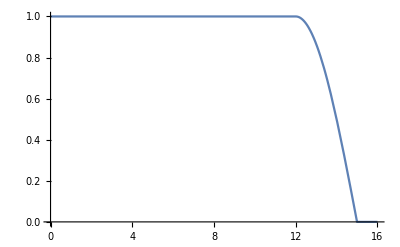

```mathematica
Plot[windowFunction[x],{x,0,16},PlotRange->All]
```

Compute the weight at each point in the Fourier domain

```mathematica
fourierWindowWeights=Map[windowFunction[Norm[#]]&,N[fourierPoints],{3}];
```

Define a function for applying the weights in the Fourier domain

```mathematica
filteredImage[img_]:=Chop[InverseFourier[Fourier[img,FourierParameters->{1, -1}] * fourierWindowWeights,FourierParameters->{1, -1}]];
```

Apply the Fourier-domain weights to each image volume

```mathematica
filteredRefVolScaled=filteredImage[refVolScaled];
```

```mathematica
filteredNewVolScaled=filteredImage[newVolScaled];
```

```mathematica
points=Function[{zDim,yDim,xDim},Table[{i-(zDim/2-0.5),j-(yDim/2-0.5),k-(xDim/2-0.5)},{i,0,zDim-1},{j,0,yDim-1},{k,0,xDim-1}]]@@{32,32,32};
```

```mathematica
pointWeights=(windowFunction[Norm[#]]&/@Flatten[points,2]);
```

```mathematica
z1=N[-2+Sqrt[3]]
```

-0.267949

```mathematica
c0=6;
```

```mathematica
computeG[x_,dataLength_]:=MapThread[Times,{FoldList[z1#1+#2&,x*c0],PadLeft[{1/(1-z1^dataLength)},dataLength,1]}]
```

```mathematica
computeYPlus[x_,dataLength_]:=Function[list,Append[MapIndexed[#1+z1^(#2[[1]])Last[list]&,list][[;;-2]],Last[list]]]@computeG[x,dataLength]
```

```mathematica
computeH[x_,dataLength_]:=Reverse[MapThread[Times,{FoldList[z1#1+#2&,Reverse[-z1 computeYPlus[x,dataLength]]]PadLeft[{1/(1-z1^dataLength)},dataLength,1]}]]
```

```mathematica
computeY[x_,dataLength_]:=Reverse[Function[list,Append[MapIndexed[#1+z1^(#2[[1]])Last[list]&,list][[;;-2]],Last[list]]]@Reverse[computeH[x,dataLength]]]
```

```mathematica
coeffImageBSpline[img_]:=Block[{
y},
(* Do x-direction calculation *)
y = Map[computeY[#,Dimensions[img][[3]]]&,img,{2}];
(* Do y-direction calculation *)
y = Map[computeY[#,Dimensions[y][[2]]]&,y];
(* Do z-direction calculation *)
y = computeY[y,Dimensions[y][[1]]];
Return[y];
];
```

This is the coefficient matrix that links the 64 coefficient values in the neighbourhood around a point, with the 64 powers of that point’s coordinates inside the cell..

```mathematica
bSplineCoeffMat={{1/216,1/54,1/216,0,1/54,2/27,1/54,0,1/216,1/54,1/216,0,0,0,0,0,1/54,2/27,1/54,0,2/27,8/27,2/27,0,1/54,2/27,1/54,0,0,0,0,0,1/216,1/54,1/216,0,1/54,2/27,1/54,0,1/216,1/54,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,0,1/72,0,-1/18,0,1/18,0,-1/72,0,1/72,0,0,0,0,0,-1/18,0,1/18,0,-2/9,0,2/9,0,-1/18,0,1/18,0,0,0,0,0,-1/72,0,1/72,0,-1/18,0,1/18,0,-1/72,0,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/36,1/72,0,1/18,-1/9,1/18,0,1/72,-1/36,1/72,0,0,0,0,0,1/18,-1/9,1/18,0,2/9,-4/9,2/9,0,1/18,-1/9,1/18,0,0,0,0,0,1/72,-1/36,1/72,0,1/18,-1/9,1/18,0,1/72,-1/36,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/216,1/72,-1/72,1/216,-1/54,1/18,-1/18,1/54,-1/216,1/72,-1/72,1/216,0,0,0,0,-1/54,1/18,-1/18,1/54,-2/27,2/9,-2/9,2/27,-1/54,1/18,-1/18,1/54,0,0,0,0,-1/216,1/72,-1/72,1/216,-1/54,1/18,-1/18,1/54,-1/216,1/72,-1/72,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,-1/18,-1/72,0,0,0,0,0,1/72,1/18,1/72,0,0,0,0,0,-1/18,-2/9,-1/18,0,0,0,0,0,1/18,2/9,1/18,0,0,0,0,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,0,-1/24,0,0,0,0,0,-1/24,0,1/24,0,0,0,0,0,1/6,0,-1/6,0,0,0,0,0,-1/6,0,1/6,0,0,0,0,0,1/24,0,-1/24,0,0,0,0,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/12,-1/24,0,0,0,0,0,1/24,-1/12,1/24,0,0,0,0,0,-1/6,1/3,-1/6,0,0,0,0,0,1/6,-1/3,1/6,0,0,0,0,0,-1/24,1/12,-1/24,0,0,0,0,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,0,0,0,0,-1/72,1/24,-1/24,1/72,0,0,0,0,1/18,-1/6,1/6,-1/18,0,0,0,0,-1/18,1/6,-1/6,1/18,0,0,0,0,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,1/18,1/72,0,-1/36,-1/9,-1/36,0,1/72,1/18,1/72,0,0,0,0,0,1/18,2/9,1/18,0,-1/9,-4/9,-1/9,0,1/18,2/9,1/18,0,0,0,0,0,1/72,1/18,1/72,0,-1/36,-1/9,-1/36,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,0,1/24,0,1/12,0,-1/12,0,-1/24,0,1/24,0,0,0,0,0,-1/6,0,1/6,0,1/3,0,-1/3,0,-1/6,0,1/6,0,0,0,0,0,-1/24,0,1/24,0,1/12,0,-1/12,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/12,1/24,0,-1/12,1/6,-1/12,0,1/24,-1/12,1/24,0,0,0,0,0,1/6,-1/3,1/6,0,-1/3,2/3,-1/3,0,1/6,-1/3,1/6,0,0,0,0,0,1/24,-1/12,1/24,0,-1/12,1/6,-1/12,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,1/36,-1/12,1/12,-1/36,-1/72,1/24,-1/24,1/72,0,0,0,0,-1/18,1/6,-1/6,1/18,1/9,-1/3,1/3,-1/9,-1/18,1/6,-1/6,1/18,0,0,0,0,-1/72,1/24,-1/24,1/72,1/36,-1/12,1/12,-1/36,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/216,-1/54,-1/216,0,1/72,1/18,1/72,0,-1/72,-1/18,-1/72,0,1/216,1/54,1/216,0,-1/54,-2/27,-1/54,0,1/18,2/9,1/18,0,-1/18,-2/9,-1/18,0,1/54,2/27,1/54,0,-1/216,-1/54,-1/216,0,1/72,1/18,1/72,0,-1/72,-1/18,-1/72,0,1/216,1/54,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,0,-1/72,0,-1/24,0,1/24,0,1/24,0,-1/24,0,-1/72,0,1/72,0,1/18,0,-1/18,0,-1/6,0,1/6,0,1/6,0,-1/6,0,-1/18,0,1/18,0,1/72,0,-1/72,0,-1/24,0,1/24,0,1/24,0,-1/24,0,-1/72,0,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/36,-1/72,0,1/24,-1/12,1/24,0,-1/24,1/12,-1/24,0,1/72,-1/36,1/72,0,-1/18,1/9,-1/18,0,1/6,-1/3,1/6,0,-1/6,1/3,-1/6,0,1/18,-1/9,1/18,0,-1/72,1/36,-1/72,0,1/24,-1/12,1/24,0,-1/24,1/12,-1/24,0,1/72,-1/36,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/216,-1/72,1/72,-1/216,-1/72,1/24,-1/24,1/72,1/72,-1/24,1/24,-1/72,-1/216,1/72,-1/72,1/216,1/54,-1/18,1/18,-1/54,-1/18,1/6,-1/6,1/18,1/18,-1/6,1/6,-1/18,-1/54,1/18,-1/18,1/54,1/216,-1/72,1/72,-1/216,-1/72,1/24,-1/24,1/72,1/72,-1/24,1/24,-1/72,-1/216,1/72,-1/72,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,-1/18,-1/72,0,-1/18,-2/9,-1/18,0,-1/72,-1/18,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,0,-1/24,0,1/6,0,-1/6,0,1/24,0,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/12,-1/24,0,-1/6,1/3,-1/6,0,-1/24,1/12,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,1/18,-1/6,1/6,-1/18,1/72,-1/24,1/24,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,1/6,1/24,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,0,1/8,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,-1/4,1/8,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/8,-1/8,1/24,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,-1/6,-1/24,0,1/12,1/3,1/12,0,-1/24,-1/6,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,0,-1/8,0,-1/4,0,1/4,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,1/4,-1/8,0,1/4,-1/2,1/4,0,-1/8,1/4,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/8,1/8,-1/24,-1/12,1/4,-1/4,1/12,1/24,-1/8,1/8,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,1/18,1/72,0,-1/24,-1/6,-1/24,0,1/24,1/6,1/24,0,-1/72,-1/18,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,0,1/24,0,1/8,0,-1/8,0,-1/8,0,1/8,0,1/24,0,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/12,1/24,0,-1/8,1/4,-1/8,0,1/8,-1/4,1/8,0,-1/24,1/12,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,1/24,-1/8,1/8,-1/24,-1/24,1/8,-1/8,1/24,1/72,-1/24,1/24,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,-1/36,-1/9,-1/36,0,-1/9,-4/9,-1/9,0,-1/36,-1/9,-1/36,0,0,0,0,0,1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,1/12,0,-1/12,0,1/3,0,-1/3,0,1/12,0,-1/12,0,0,0,0,0,-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,-1/12,1/6,-1/12,0,-1/3,2/3,-1/3,0,-1/12,1/6,-1/12,0,0,0,0,0,1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,1/36,-1/12,1/12,-1/36,1/9,-1/3,1/3,-1/9,1/36,-1/12,1/12,-1/36,0,0,0,0,-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,1/12,1/3,1/12,0,0,0,0,0,-1/12,-1/3,-1/12,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,1/4,-1/2,1/4,0,0,0,0,0,-1/4,1/2,-1/4,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,-1/12,1/4,-1/4,1/12,0,0,0,0,1/12,-1/4,1/4,-1/12,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,-1/12,-1/3,-1/12,0,1/6,2/3,1/6,0,-1/12,-1/3,-1/12,0,0,0,0,0,1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,1/4,0,-1/4,0,-1/2,0,1/2,0,1/4,0,-1/4,0,0,0,0,0,-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,-1/4,1/2,-1/4,0,1/2,-1,1/2,0,-1/4,1/2,-1/4,0,0,0,0,0,1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,1/12,-1/4,1/4,-1/12,-1/6,1/2,-1/2,1/6,1/12,-1/4,1/4,-1/12,0,0,0,0,-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,1/36,1/9,1/36,0,-1/12,-1/3,-1/12,0,1/12,1/3,1/12,0,-1/36,-1/9,-1/36,0,-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,-1/12,0,1/12,0,1/4,0,-1/4,0,-1/4,0,1/4,0,1/12,0,-1/12,0,1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,1/12,-1/6,1/12,0,-1/4,1/2,-1/4,0,1/4,-1/2,1/4,0,-1/12,1/6,-1/12,0,-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,-1/36,1/12,-1/12,1/36,1/12,-1/4,1/4,-1/12,-1/12,1/4,-1/4,1/12,1/36,-1/12,1/12,-1/36,1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/216,-1/54,-1/216,0,-1/54,-2/27,-1/54,0,-1/216,-1/54,-1/216,0,0,0,0,0,1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,-1/72,-1/18,-1/72,0,-1/18,-2/9,-1/18,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/216,1/54,1/216,0,1/54,2/27,1/54,0,1/216,1/54,1/216,0,0,0,0,0},{1/72,0,-1/72,0,1/18,0,-1/18,0,1/72,0,-1/72,0,0,0,0,0,-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,1/24,0,-1/24,0,1/6,0,-1/6,0,1/24,0,-1/24,0,0,0,0,0,-1/72,0,1/72,0,-1/18,0,1/18,0,-1/72,0,1/72,0,0,0,0,0},{-1/72,1/36,-1/72,0,-1/18,1/9,-1/18,0,-1/72,1/36,-1/72,0,0,0,0,0,1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,-1/24,1/12,-1/24,0,-1/6,1/3,-1/6,0,-1/24,1/12,-1/24,0,0,0,0,0,1/72,-1/36,1/72,0,1/18,-1/9,1/18,0,1/72,-1/36,1/72,0,0,0,0,0},{1/216,-1/72,1/72,-1/216,1/54,-1/18,1/18,-1/54,1/216,-1/72,1/72,-1/216,0,0,0,0,-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,1/72,-1/24,1/24,-1/72,1/18,-1/6,1/6,-1/18,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/216,1/72,-1/72,1/216,-1/54,1/18,-1/18,1/54,-1/216,1/72,-1/72,1/216,0,0,0,0},{1/72,1/18,1/72,0,0,0,0,0,-1/72,-1/18,-1/72,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/72,1/18,1/72,0,0,0,0,0},{-1/24,0,1/24,0,0,0,0,0,1/24,0,-1/24,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,1/24,0,-1/24,0,0,0,0,0,-1/24,0,1/24,0,0,0,0,0},{1/24,-1/12,1/24,0,0,0,0,0,-1/24,1/12,-1/24,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,-1/24,1/12,-1/24,0,0,0,0,0,1/24,-1/12,1/24,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,0,0,0,0,1/72,-1/24,1/24,-1/72,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/72,1/24,-1/24,1/72,0,0,0,0},{-1/72,-1/18,-1/72,0,1/36,1/9,1/36,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,-1/24,-1/6,-1/24,0,1/12,1/3,1/12,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/72,1/18,1/72,0,-1/36,-1/9,-1/36,0,1/72,1/18,1/72,0,0,0,0,0},{1/24,0,-1/24,0,-1/12,0,1/12,0,1/24,0,-1/24,0,0,0,0,0,-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,1/8,0,-1/8,0,-1/4,0,1/4,0,1/8,0,-1/8,0,0,0,0,0,-1/24,0,1/24,0,1/12,0,-1/12,0,-1/24,0,1/24,0,0,0,0,0},{-1/24,1/12,-1/24,0,1/12,-1/6,1/12,0,-1/24,1/12,-1/24,0,0,0,0,0,1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,-1/8,1/4,-1/8,0,1/4,-1/2,1/4,0,-1/8,1/4,-1/8,0,0,0,0,0,1/24,-1/12,1/24,0,-1/12,1/6,-1/12,0,1/24,-1/12,1/24,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,-1/36,1/12,-1/12,1/36,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,1/24,-1/8,1/8,-1/24,-1/12,1/4,-1/4,1/12,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/72,1/24,-1/24,1/72,1/36,-1/12,1/12,-1/36,-1/72,1/24,-1/24,1/72,0,0,0,0},{1/216,1/54,1/216,0,-1/72,-1/18,-1/72,0,1/72,1/18,1/72,0,-1/216,-1/54,-1/216,0,-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,1/72,1/18,1/72,0,-1/24,-1/6,-1/24,0,1/24,1/6,1/24,0,-1/72,-1/18,-1/72,0,-1/216,-1/54,-1/216,0,1/72,1/18,1/72,0,-1/72,-1/18,-1/72,0,1/216,1/54,1/216,0},{-1/72,0,1/72,0,1/24,0,-1/24,0,-1/24,0,1/24,0,1/72,0,-1/72,0,1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,-1/24,0,1/24,0,1/8,0,-1/8,0,-1/8,0,1/8,0,1/24,0,-1/24,0,1/72,0,-1/72,0,-1/24,0,1/24,0,1/24,0,-1/24,0,-1/72,0,1/72,0},{1/72,-1/36,1/72,0,-1/24,1/12,-1/24,0,1/24,-1/12,1/24,0,-1/72,1/36,-1/72,0,-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,1/24,-1/12,1/24,0,-1/8,1/4,-1/8,0,1/8,-1/4,1/8,0,-1/24,1/12,-1/24,0,-1/72,1/36,-1/72,0,1/24,-1/12,1/24,0,-1/24,1/12,-1/24,0,1/72,-1/36,1/72,0},{-1/216,1/72,-1/72,1/216,1/72,-1/24,1/24,-1/72,-1/72,1/24,-1/24,1/72,1/216,-1/72,1/72,-1/216,1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,-1/72,1/24,-1/24,1/72,1/24,-1/8,1/8,-1/24,-1/24,1/8,-1/8,1/24,1/72,-1/24,1/24,-1/72,1/216,-1/72,1/72,-1/216,-1/72,1/24,-1/24,1/72,1/72,-1/24,1/24,-1/72,-1/216,1/72,-1/72,1/216}};
```

Define a function that takes and image and all of its derivatives, and computes the interpolation coefficients

```mathematica
coeffs[img_]:=Transpose[bSplineCoeffMat. Function[coeffImg,RotateLeft[coeffImg,#]&/@Flatten[Table[{k,j,i},{k,-1,2},{j,-1,2},{i,-1,2}],2]]@(coeffImageBSpline[img]),{4,1,2,3}];
```

Define a function that takes a set of interpolation coefficients, a rotation matrix, a translation vector (and the dimensions of the image volume), and interpolates the image at a set of points

```mathematica
transformPoints[rotMatrix_,trans_,points_,dims_,halfDims_]:=
Block[{invRot=Inverse[rotMatrix]},
Return[Map[invRot . (#-trans)&,points,{3}]];
]
```

```mathematica
interpImg[coeffs_,interpGridPoints_,dims_,halfDims_]:=
Block[{
curInterpGridPoint=(Mod[# + halfDims - {0.5,0.5,0.5}+dims,dims]+{1,1,1})&/@Flatten[interpGridPoints,2],
coeffIndices,interVoxelPoints,interVoxelPointPowers},
coeffIndices=Floor[curInterpGridPoint];
interVoxelPoints=curInterpGridPoint-coeffIndices;
interVoxelPointPowers[interVoxelPoint_]:=Flatten[Outer@@Prepend[(Transpose[{{1,1,1},interVoxelPoint,interVoxelPoint^2,interVoxelPoint^3}]),Times]];
Return[
MapThread[
Function[{coeffIndex,interVoxelPoint},(coeffs[[#1,#2,#3]] &@@coeffIndex). interVoxelPointPowers[interVoxelPoint]],
{coeffIndices,interVoxelPoints}]];
]
```

```mathematica
interpImg[coeffs_,rotMatrix_,trans_,points_,dims_,halfDims_]:=
interpImg[coeffs,transformPoints[rotMatrix,trans,points,dims,halfDims],dims,halfDims];
```

```mathematica
Dimensions[coeffs[refVolScaled]]
```

{32,32,32,64}

Compute the cooridinates of each voxel in the image domain; note that image coordinates put the origin at the center of the image, so each voxel has a non-integer coordinate.

```mathematica
points=Function[{zDim,yDim,xDim},Table[{i-(zDim/2-0.5),j-(yDim/2-0.5),k-(xDim/2-0.5)},{i,0,zDim-1},{j,0,yDim-1},{k,0,xDim-1}]]@@{32,32,32};
```

```mathematica
Dimensions[points]
```

{32,32,32,3}

```mathematica
Dimensions[transformPoints[IdentityMatrix[3],{0,0,0},points,{32,32,32},{16,16,16}]]
```

{32,32,32,3}

```mathematica
Dimensions[interpImg[coeffs[refVolScaled],IdentityMatrix[3],{0,0,0},points,{32,32,32},{16,16,16}]]
```

{32768}

```mathematica
derivs[img_]:=Block[{
y,
derivX,
derivY,
derivZ},
(* Compute x-direction derivs *)
derivX=(RotateRight[img,{0,0,-1}]-RotateRight[img,{0,0,1}])/2;
(* Compute x-direction derivs *)
derivY=(RotateRight[img,{0,-1,0}]-RotateRight[img,{0,1,0}])/2;
derivZ=(RotateRight[img,{-1,0,0}]-RotateRight[img,{1,0,0}])/2;
Return[{derivX, derivY, derivZ}];
];
```

6D Registration

We want to find the linear approximation to the derivatives with respect to how an object rotating around a vector x by norm[x] radians, and then translating, will change the image. The M matrix represents this approximation, and is a function of the coordinate at which its being evaluated, so define a method to compute it given the coordinate. Note that because we’re describing the effect of moving the object, the signs are flipped vs in Martin’s paper. Also note that because my derivatives are stored in the order (dx, dy, dz), but my coordinates in the p-vector are (z,y,x,rz,ry,rx) I need to reverse the order of the rows vs in Martin’s paper.

```mathematica
M[x_]:= {{0,0,-1,-x[[2]],x[[1]],0},{0,-1,0,x[[3]],0,-x[[1]]},{-1,0,0,0,-x[[3]],x[[2]]}} ;
```

```mathematica
M[{z,y,x}]//MatrixForm
```

(0 | 0 | -1 | -y | z | 0
0 | -1 | 0 | x | 0 | -z
-1 | 0 | 0 | 0 | -x | y)

Compute the M matrix for every point in the image, giving an M tensor

```mathematica
MTensor[points_]:=Transpose[Map[M,points,{3}],{1,2,3,5,4}];
```

```mathematica
Dimensions[MTensor[points]]
```

{32,32,32,6,3}

Visualize the derivatives of the first image volume with respect to the six parameters

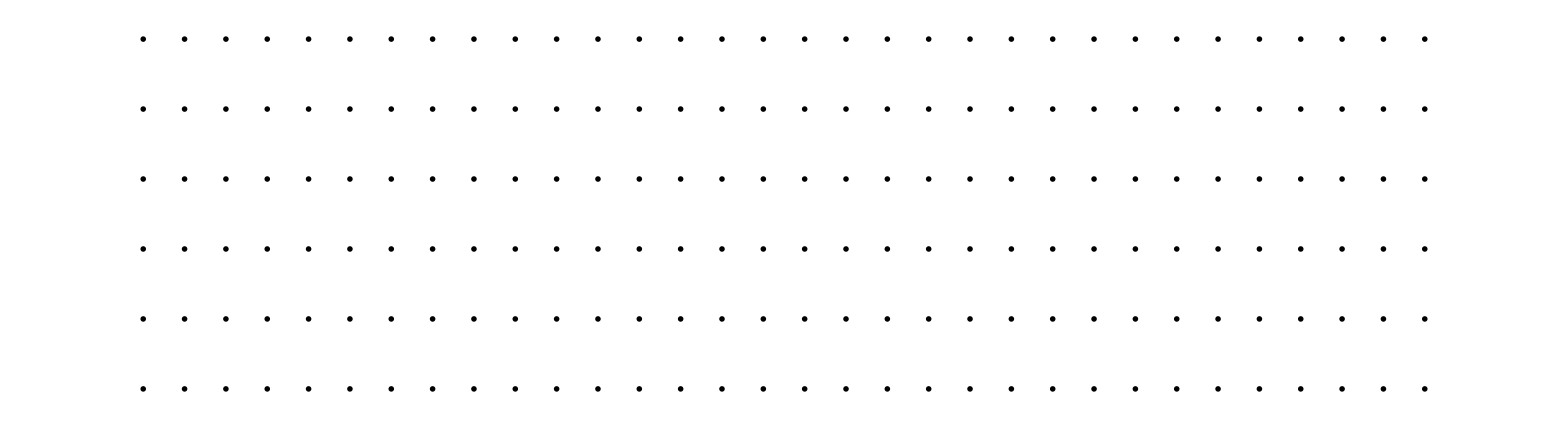

```mathematica
GraphicsGrid[Map[ArrayPlot[#,PixelConstrained->2]&,#/(2Max[#])+0.5,{2}]&@(Transpose[Partition[Partition[Flatten[MapThread[#1 . #2&,{MTensor[points],Transpose[derivs[filteredRefVolScaled],{4,1,2,3}]},3],2],32],32],{2,3,4,1}])]
```

```mathematica
Dimensions[(Transpose[Partition[Partition[Flatten[MapThread[#1 . #2&,{MTensor[points],Transpose[derivs[filteredRefVolScaled],{4,1,2,3}]},3],2],32],32],{2,3,4,1}])]
```

{6,32,32,32}

Given the gradient with respect to p, and the residual r, compute a Gauss Newton step

```mathematica
GaussNewtonStep[gradPTransGradP_,gradP_,r_]:=Block[
{deltaP,
JTransR=-Transpose[gradP] . r},
(*Print["JTransR" <> ToString[JTransR]];*)
deltaP=LinearSolve[gradPTransGradP,JTransR];
Return[deltaP]]
```

Define a utility function that takes a value of p, and prints the length of the translations in mm, the translation vector in mm, the angle of rotation in degrees, and the axis of rotation.

```mathematica
pToTransAndRot[p_]:={{Norm[p[[1;;3]]*8],p[[1;;3]]*8},{If[Norm[p[[4;;6]]]==0,0,Norm[p[[4;;6]]]/Degree],Normalize[p[[4;;6]]]}}
```

For clarity and debugging-value, let’s break these steps out and save the intermediate results in files, without all the trimming, etc.:

```mathematica
Norm[pointWeights *(Flatten[filteredRefVolScaled]-Flatten[filteredNewVolScaled])]
```

2.81664

```mathematica
Max[filteredRefVolScaled]
```

0.900536

```mathematica
Min[filteredRefVolScaled]
```

-0.0322055

```mathematica
Max[filteredNewVolScaled]
```

0.937795

```mathematica
Min[filteredNewVolScaled]
```

-0.0393063

```mathematica
Block[{
targetImg=filteredRefVolScaled,
movingImg=filteredNewVolScaled,
curPoints=points,
targetImgCoeffs,
residualGradP,
gradPTransGradP,
r,
prevNormR=$MaxMachineNumber,
deltaP,
p={0,0,0,0,0,0},
pList},
(* compute and save the interpolation coefficients for the target image *)
targetImgCoeffs=coeffs[targetImg];
(*Print["TargetImgCoeffs dimensions: " <>ToString[Dimensions[targetImgCoeffs]]];*)
(* compute and save the gradient of the moving image with respect to p *)
residualGradP=Transpose[(pointWeights * #)&/@Transpose[Flatten[MapThread[#1 . #2&,{MTensor[curPoints],Transpose[derivs[movingImg],{4,1,2,3}]},3],2]]];
(*Print["residualGradP[[1]]: " <>ToString[residualGradP[[1]]]];*)
gradPTransGradP=Transpose[residualGradP]. residualGradP;
(*Print["gradPTransGradP: " <>ToString[gradPTransGradP]];*)
(* now start the optimization *)
pList={p};
For[i=0,i<20,i++,
(* Compute and save the residual vector by: 1) interpolating the target image at all the points based on the current p, 2) subtracting this from the moving image, 3) multiplying this difference by the weights *)
(*Print[Dimensions[Flatten[points,2]]];*)
r=pointWeights *(interpImg[targetImgCoeffs,If[Norm[p[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[p[[4;;6]]],p[[4;;6]]]],p[[1;;3]],points,{32,32,32},{16,16,16}]-Flatten[movingImg]);
(*Print["r[[1]] " <> ToString[r[[1]]]];*)
(*Print["R_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[r]]];*)
(* take a Gauss Newton step, save the deltaP, and update p *)
Print[Norm[r]];
If[Norm[r]>prevNormR, 
pList=pList[[;;-2]];Break[],
prevNormR = Norm[r]];
deltaP = GaussNewtonStep[gradPTransGradP,residualGradP,r];
(*Print["DeltaP_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[deltaP]]];*)
p=p+deltaP;
(* append this new p to our list of previous states *)
pList=Append[pList,p];
Print[p];
Print[pToTransAndRot[p]]
];
BinaryWrite[NotebookDirectory[]<>"parameterOutput.dat",Last[pList],"Real64"]
]
```

2.81664

{-0.00578503,-0.047937,0.0199367,-0.0475393,0.000824677,0.000235509}

{{0.41791,{-0.0462803,-0.383496,0.159493}},{2.72424,{-0.999837,0.0173444,0.00495318}}}

1.63189

{-0.00430664,-0.0349291,0.0082324,-0.0373964,0.00032326,0.000466848}

{{0.289149,{-0.0344532,-0.279432,0.0658592}},{2.1429,{-0.999885,0.00864314,0.0124823}}}

1.52505

{-0.00479158,-0.038255,0.0105404,-0.0403073,0.000482706,0.000406186}

{{0.31975,{-0.0383327,-0.30604,0.084323}},{2.30972,{-0.999878,0.0119742,0.010076}}}

1.52348

{-0.00464014,-0.037331,0.00998104,-0.0394747,0.000429729,0.000424315}

{{0.311359,{-0.0371211,-0.298648,0.0798483}},{2.262,{-0.999883,0.0108849,0.0107478}}}

1.52139

{-0.00468566,-0.0375907,0.0101186,-0.0397127,0.000446304,0.000418977}

{{0.313678,{-0.0374852,-0.300726,0.0809484}},{2.27564,{-0.999881,0.011237,0.010549}}}

1.52178

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_New_Grad_tests/parameterOutput.dat

```mathematica
Close[NotebookDirectory[]<>"parameterOutput.dat"]
```

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_New_Grad_tests/parameterOutput.dat

```mathematica
Block[{
targetImg=filteredRefVolScaled,
movingImg=filteredNewVolScaled,
dims={32,32,32},
halfDims={16,16,16},
sourceDerivs=Transpose[derivs[filteredNewVolScaled],{4,1,2,3}],
curPoints=points,
targetImgCoeffs,
residualGradP,
gradPTransGradP,
r,
prevNormR=$MaxMachineNumber,
deltaP,
p={0,0,0,0,0,0},
pList},
(* compute and save the interpolation coefficients for the target image *)
targetImgCoeffs=coeffs[targetImg];
(*Print["TargetImgCoeffs dimensions: " <>ToString[Dimensions[targetImgCoeffs]]];*)
(* compute and save the gradient of the moving image with respect to p *)
(*Print["gradPTransGradP: " <>ToString[gradPTransGradP]];*)
(* now start the optimization *)
pList={p};
For[i=0,i<20,i++,
(* Compute and save the residual vector by: 1) interpolating the target image at all the points based on the current p, 2) subtracting this from the moving image, 3) multiplying this difference by the weights *)
(*Print[Dimensions[Flatten[points,2]]];*)
curPoints=transformPoints[
If[Norm[p[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[p[[4;;6]]],p[[4;;6]]]],
p[[1;;3]],
points,
dims,halfDims];
r=pointWeights *(interpImg[targetImgCoeffs,curPoints,dims,halfDims]-Flatten[movingImg]);
(*Print["r[[1]] " <> ToString[r[[1]]]];*)
(*Print["R_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[r]]];*)
(* take a Gauss Newton step, save the deltaP, and update p *)
Print[Norm[r]];
If[Norm[r]>prevNormR, 
pList=pList[[;;-2]];Break[],
prevNormR = Norm[r]];
residualGradP=Transpose[(pointWeights * #)&/@Transpose[Flatten[MapThread[#1 . #2&,{MTensor[curPoints],Transpose[derivs[movingImg],{4,1,2,3}]},3],2]]];
gradPTransGradP=Transpose[residualGradP]. residualGradP;
deltaP = GaussNewtonStep[gradPTransGradP,residualGradP,r];
(*Print["DeltaP_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[deltaP]]];*)
p=p+deltaP;
(* append this new p to our list of previous states *)
pList=Append[pList,p];
Print[p];
Print[pToTransAndRot[p]]
];
BinaryWrite[NotebookDirectory[]<>"gradientUpdateParameterOutput.dat",Last[pList],"Real64"]
]
```

2.81664

{-0.00578503,-0.047937,0.0199367,-0.0475393,0.000824677,0.000235509}

{{0.41791,{-0.0462803,-0.383496,0.159493}},{2.72424,{-0.999837,0.0173444,0.00495318}}}

1.63189

{-0.00427671,-0.0347491,0.00783915,-0.0374532,0.000341179,0.000404933}

{{0.287025,{-0.0342137,-0.277993,0.0627132}},{2.14613,{-0.9999,0.00910857,0.0108106}}}

1.52491

{-0.00480139,-0.0383634,0.010734,-0.0402615,0.000463942,0.000425318}

{{0.321001,{-0.0384112,-0.306907,0.0858716}},{2.30709,{-0.999878,0.0115218,0.0105626}}}

1.52341

{-0.00463683,-0.0373364,0.00998117,-0.0394725,0.000427472,0.000411644}

{{0.311397,{-0.0370947,-0.298691,0.0798493}},{2.26186,{-0.999887,0.0108284,0.0104274}}}

1.52139

{-0.00468543,-0.0376262,0.0101791,-0.039694,0.000437703,0.000417187}

{{0.314075,{-0.0374834,-0.30101,0.081433}},{2.27456,{-0.999884,0.0110257,0.0105089}}}

1.52177

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_New_Grad_tests/gradientUpdateParameterOutput.dat

```mathematica
Close[NotebookDirectory[]<>"gradientUpdateParameterOutput.dat"]
```

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_New_Grad_tests/gradientUpdateParameterOutput.dat

This axisAngle method is taken from http://mathematica.stackexchange.com/questions/29924/axis-angle-from-rotation-matrix

```mathematica
axisAngle[m_]:=Module[{axis,ovec,nvec},{axis,ovec}=Orthogonalize[{{1,-1,1} #,Permute[#,Cycles[{{1,3,2}}]]}]&@Extract[m-Transpose[m],{{3,2},{3,1},{2,1}}];
(*nvec is orthogonal to axis and ovec:*)nvec=Cross[axis,ovec];
{axis,Arg[Complex@@(((m.ovec).#&)/@{ovec,nvec})]}]
```

```mathematica
axisAngle[IdentityMatrix[3]]
```

{{0,0,0},0}

```mathematica
AccumulateParam[deltaParam_, oldParam_]:= Block[{
oldRotationMatrix=If[Norm[oldParam[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[oldParam[[4;;6]]],oldParam[[4;;6]]]],
deltaRotationMatrix=If[Norm[deltaParam[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[deltaParam[[4;;6]]],deltaParam[[4;;6]]]],
newRotationMatrix,
newRotationAxis,
newRotationAngle},
newRotationMatrix = oldRotationMatrix . deltaRotationMatrix;
{newRotationAxis, newRotationAngle}=axisAngle[newRotationMatrix];
Return[Join[oldRotationMatrix . deltaParam[[1;;3]]+oldParam[[1;;3]], newRotationAxis * newRotationAngle]];
]
```

```mathematica
Block[{
targetImg=filteredRefVolScaled,
movingImg=filteredNewVolScaled,
dims={32,32,32},
halfDims={16,16,16},
sourceDerivs=Transpose[derivs[filteredNewVolScaled],{4,1,2,3}],
curPoints=points,
targetImgCoeffs,
residualGradP,
gradPTransGradP,
r,
prevNormR=$MaxMachineNumber,
deltaP,
p={0,0,0,0,0,0},
pList},
(* compute and save the interpolation coefficients for the target image *)
targetImgCoeffs=coeffs[targetImg];
(*Print["TargetImgCoeffs dimensions: " <>ToString[Dimensions[targetImgCoeffs]]];*)
(* compute and save the gradient of the moving image with respect to p *)
(*Print["gradPTransGradP: " <>ToString[gradPTransGradP]];*)
(* now start the optimization *)
pList={p};
For[i=0,i<20,i++,
(* Compute and save the residual vector by: 1) interpolating the target image at all the points based on the current p, 2) subtracting this from the moving image, 3) multiplying this difference by the weights *)
(*Print[Dimensions[Flatten[points,2]]];*)
curPoints=transformPoints[
If[Norm[p[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[p[[4;;6]]],p[[4;;6]]]],
p[[1;;3]],
points,
dims,halfDims];
r=pointWeights *(interpImg[targetImgCoeffs,curPoints,dims,halfDims]-Flatten[movingImg]);
(*Print["r[[1]] " <> ToString[r[[1]]]];*)
(*Print["R_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[r]]];*)
(* take a Gauss Newton step, save the deltaP, and update p *)
Print[Norm[r]];
If[Norm[r]>prevNormR, 
pList=pList[[;;-2]];Break[],
prevNormR = Norm[r]];
residualGradP=Transpose[(pointWeights * #)&/@Transpose[Flatten[MapThread[#1 . #2&,{MTensor[curPoints],Transpose[derivs[movingImg],{4,1,2,3}]},3],2]]];
gradPTransGradP=Transpose[residualGradP]. residualGradP;
deltaP = GaussNewtonStep[gradPTransGradP,residualGradP,r];
(*Print["DeltaP_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[deltaP]]];*)
p=AccumulateParam[deltaP,p];
(* append this new p to our list of previous states *)
pList=Append[pList,p];
Print[p];
Print[pToTransAndRot[p]]
];
BinaryWrite[NotebookDirectory[]<>"gradientUpdateComposeAccumulateParameterOutput.dat",Last[pList],"Real64"]
]
```

2.81664

{-0.00578503,-0.047937,0.0199367,-0.0475393,0.000824677,0.000235509}

{{0.41791,{-0.0462803,-0.383496,0.159493}},{2.72424,{-0.999837,0.0173444,0.00495318}}}

1.63189

{-0.00428998,-0.0353386,0.00722486,-0.0374531,0.000346465,0.000412216}

{{0.29059,{-0.0343198,-0.282708,0.0577989}},{2.14613,{-0.999897,0.00924966,0.011005}}}

1.52494

{-0.00480185,-0.0381327,0.0109619,-0.0402559,0.000462317,0.000422967}

{{0.319732,{-0.0384148,-0.305061,0.0876951}},{2.30677,{-0.999879,0.0114831,0.0105057}}}

1.52339

{-0.00463565,-0.0374162,0.00990757,-0.039476,0.000427796,0.000412332}

{{0.311859,{-0.0370852,-0.29933,0.0792606}},{2.26207,{-0.999887,0.0108356,0.010444}}}

1.5214

{-0.00468605,-0.0376015,0.0102008,-0.0396923,0.000437667,0.000417001}

{{0.313931,{-0.0374884,-0.300812,0.0816063}},{2.27446,{-0.999884,0.0110252,0.0105046}}}

1.52176

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_New_Grad_tests/gradientUpdateComposeAccumulateParameterOutput.dat

```mathematica
Close[NotebookDirectory[]<>"gradientUpdateComposeAccumulateParameterOutput.dat"]
```

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_New_Grad_tests/gradientUpdateComposeAccumulateParameterOutput.dat